```mathematica
(*css zebrafinch model with V excluded numerical solution*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs(lsI vI z +lsO qO ) + nh vh(lhI vI z +lhO qO );
NNn :=ns vs(lsI vI (1-z)+lsO(1- qO) ) + nh vh(lhI vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
(*matrix of transition probabilities*)AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs(lsI vI z +lsO qO ), vh(lhI vI z +lhO qO ), 0, 0}, {vs(lsI vI (1-z)+lsO(1- qO) ), vh(lhI vI (1-z)+lhO(1- qO) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa]/.{lhV -> 0, lsV->0};
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z-√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))},{Fa→(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z+√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))}}

```mathematica
subtest = {ba->2,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.7,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2 ,u-> 0.03 };
sub =  {ba->2,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.7,vh->0.95,vI->0.7  ,u-> 0.03 };
```

```mathematica
Fasols[[2,1,2]]/.subtest (*check it is stable qhat*)
```

0.55725

```mathematica
Qhat =  Fasols[[2,1,2]]/.sub
```

(0.6118 lhI-0.00285 lhO-0.6468 lsI+√(-4 (-0.0399 lhI-0.2646 lsI) (1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)+(-0.6118 lhI+0.00285 lhO+0.6468 lsI+0.0189 lsO)^2)-0.0189 lsO)/(2 (1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO))

```mathematica
AA2=AA/.{Na->Qhat,Nn->(1-Qhat)}/.sub/.{pa->0,pn->1}
```

{{0,0,0.2,0.9},{0,0,1.8,0.1},{0.7 (0.42 lsI+(0.485 (0.6118 lhI-0.00285 lhO-0.6468 lsI+√(-4 (-0.0399 lhI-0.2646 lsI) (1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)+(-0.6118 lhI+0.00285 lhO+0.6468 lsI+0.0189 lsO)^2)-0.0189 lsO) lsO)/(1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)),0.95 (0.42 lhI+(0.485 lhO (0.6118 lhI-0.00285 lhO-0.6468 lsI+√(-4 (-0.0399 lhI-0.2646 lsI) (1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)+(-0.6118 lhI+0.00285 lhO+0.6468 lsI+0.0189 lsO)^2)-0.0189 lsO))/(1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)),0,0},{0.7 (0.28 lsI+(1-(0.485 (0.6118 lhI-0.00285 lhO-0.6468 lsI+√(-4 (-0.0399 lhI-0.2646 lsI) (1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)+(-0.6118 lhI+0.00285 lhO+0.6468 lsI+0.0189 lsO)^2)-0.0189 lsO))/(1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)) lsO),0.95 (0.28 lhI+lhO (1-(0.485 (0.6118 lhI-0.00285 lhO-0.6468 lsI+√(-4 (-0.0399 lhI-0.2646 lsI) (1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO)+(-0.6118 lhI+0.00285 lhO+0.6468 lsI+0.0189 lsO)^2)-0.0189 lsO))/(1.1305 lhI+0.04845 lhO-0.343 lsI-0.0147 lsO))),0,0}}

```mathematica
LL=Eigenvalues[AA2]
```

{(0.00025 Root[355+(1) #1^2+#1^4&,1])/(-22610. lhI-969. lhO+6860. lsI+294. lsO),(0.00025 Root[356+#1^4&,2])/(-22610. lhI-969. lhO+6860. lsI+294. lsO),(0.00025 Root[1&,3])/(-22610. lhI-969. lhO+6860. lsI+294. lsO),(0.00025 Root[355+1+#1^4&,4])/(-22610. lhI-969. lhO+6860. lsI+294. lsO)}
 |  |  |  |

```mathematica
LL/.subtest;
```

```mathematica
Simplify[LL[[2]]]
```

-((1.10571×10^-8 Root[-(1.68187×10^31 lhI^6 lhO lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.94626×10^30 lhI^5 lhO^2 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.96539×10^29 lhI^4 lhO^3 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.78927×10^28 lhI^3 lhO^4 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.34027×10^27 lhI^2 lhO^5 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.50726×10^25 lhI lhO^6 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.94065×10^23 lhO^7 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.07587×10^31 lhI^5 lhO lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.39103×10^30 lhI^4 lhO^2 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.42894×10^29 lhI^3 lhO^3 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.673×10^28 lhI^2 lhO^4 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.46996×10^26 lhI lhO^5 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.18177×10^24 lhO^6 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.2518×10^15 lhI^5 lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(8.26778×10^30 lhI^4 lhO lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.9894×10^30 lhI^3 lhO^2 lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.64666×10^29 lhI^2 lhO^3 lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.75546×10^27 lhI lhO^4 lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.29235×10^25 lhO^5 lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.6295×10^14 lhI^4 lsI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.19511×10^29 lhI^3 lhO lsI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.14648×10^29 lhI^2 lhO^2 lsI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.66378×10^28 lhI lhO^3 lsI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.43949×10^26 lhO^4 lsI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.40737×10^14 lhI^3 lsI^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.15678×10^29 lhI^2 lhO lsI^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.64417×10^28 lhI lhO^2 lsI^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.37886×10^24 lhO^3 lsI^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.58264×10^29 lhI lhO lsI^6)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.18496×10^27 lhO^2 lsI^6)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.22276×10^28 lhO lsI^7)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.68187×10^31 lhI^7 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.94626×10^30 lhI^6 lhO lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.96539×10^29 lhI^5 lhO^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.78927×10^28 lhI^4 lhO^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.34027×10^27 lhI^3 lhO^4 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.50726×10^25 lhI^2 lhO^5 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.94065×10^23 lhI lhO^6 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(69771.7 lhO^7 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.07587×10^31 lhI^6 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.31282×10^30 lhI^5 lhO lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.71447×10^29 lhI^4 lhO^2 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.59537×10^12 lhI^3 lhO^3 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.46996×10^26 lhI^2 lhO^4 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.47271×10^25 lhI lhO^5 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.92194×10^23 lhO^6 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(8.26778×10^30 lhI^5 lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(9.947×10^29 lhI^4 lhO lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.48885×10^28 lhI^3 lhO^2 lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.15109×10^28 lhI^2 lhO^3 lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.10464×10^26 lhI lhO^4 lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.21554×10^24 lhO^5 lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.19511×10^29 lhI^4 lsI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.40794×10^15 lhI^3 lhO lsI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.32756×10^28 lhI^2 lhO^2 lsI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.75159×10^27 lhI lhO^3 lsI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.78847×10^25 lhO^4 lsI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(6.15678×10^29 lhI^3 lsI^4 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.64417×10^28 lhI^2 lhO lsI^4 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.6652×10^25 lhI lhO^2 lsI^4 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(9.63172×10^25 lhO^3 lsI^4 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.58264×10^29 lhI^2 lsI^5 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.07398×10^28 lhI lhO lsI^5 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.68683×10^26 lhO^2 lsI^5 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.22276×10^28 lhI lsI^6 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.65947×10^27 lhO lsI^6 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.07821×10^30 lhI^6 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.71447×10^29 lhI^5 lhO lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.673×10^28 lhI^4 lhO^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.29399×10^27 lhI^3 lhO^3 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.09088×10^25 lhI^2 lhO^4 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.92194×10^23 lhI lhO^5 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.58518×10^7 lhO^6 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(9.947×10^29 lhI^5 lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.9211×10^29 lhI^4 lhO lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.15109×10^28 lhI^3 lhO^2 lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.45847×10^26 lhI^2 lhO^3 lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.21554×10^24 lhI lhO^4 lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.75296×10^23 lhO^5 lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.14648×10^29 lhI^4 lsI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.32756×10^28 lhI^3 lhO lsI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.71853×10^12 lhI^2 lhO^2 lsI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.15769×10^26 lhI lhO^3 lsI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.06632×10^24 lhO^4 lsI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.28834×10^28 lhI^3 lsI^3 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.75772×10^24 lhI^2 lhO lsI^3 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.92634×10^26 lhI lhO^2 lsI^3 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.24099×10^25 lhO^3 lsI^3 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.59248×10^28 lhI^2 lsI^4 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.68683×10^26 lhI lhO lsI^4 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.65402×10^25 lhO^2 lsI^4 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.65947×10^27 lhI lsI^5 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.33004×10^26 lhO lsI^5 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.74443×10^28 lhI^5 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.75546×10^27 lhI^4 lhO lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.37541×10^26 lhI^3 lhO^2 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.44311×10^25 lhI^2 lhO^3 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.75296×10^23 lhI lhO^4 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.98456×10^7 lhO^5 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.66378×10^28 lhI^4 lsI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.75159×10^27 lhI^3 lhO lsI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.15769×10^26 lhI^2 lhO^2 lsI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.38449×10^9 lhI lhO^3 lsI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.21695×10^22 lhO^4 lsI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.42731×10^25 lhI^3 lsI^2 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.92634×10^26 lhI^2 lhO lsI^2 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.13662×10^24 lhI lhO^2 lsI^2 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.32225×10^23 lhO^3 lsI^2 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.53737×10^27 lhI^2 lsI^3 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.57341×10^11 lhI lhO lsI^3 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.08284×10^23 lhO^2 lsI^3 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.33004×10^26 lhI lsI^4 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.03465×10^25 lhO lsI^4 lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.43949×10^26 lhI^4 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.78847×10^25 lhI^3 lhO lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.06632×10^24 lhI^2 lhO^2 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.21695×10^22 lhI lhO^3 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(8.38861×10^6 lhO^4 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(9.63172×10^25 lhI^3 lsI lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.44782×10^25 lhI^2 lhO lsI lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.66113×10^23 lhI lhO^2 lsI lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.6059×10^21 lhO^3 lsI lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.65402×10^25 lhI^2 lsI^2 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.54142×10^23 lhI lhO lsI^2 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.03452×10^22 lhO^2 lsI^2 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.03465×10^25 lhI lsI^3 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.37166×10^23 lhO lsI^3 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.06831×10^24 lhI^3 lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.66113×10^23 lhI^2 lhO lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(7.6059×10^21 lhI lhO^2 lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.54142×10^23 lhI^2 lsI lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.62761×10^22 lhI lhO lsI lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.05398×10^20 lhO^2 lsI lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.37166×10^23 lhI lsI^2 lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.43027×10^21 lhO lsI^2 lsO^5)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.06903×10^21 lhI^2 lsO^6)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.05398×10^20 lhI lhO lsO^6)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.43027×10^21 lhI lsI lsO^6)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.67739×10^18 lhO lsI lsO^6)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.67739×10^18 lhI lsO^7)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.13773×10^31 lhI^5 lhO lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.58085×10^30 lhI^4 lhO^2 lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.92644×10^29 lhI^3 lhO^3 lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.68276×10^28 lhI^2 lhO^4 lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.60592×10^26 lhI lhO^5 lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.09079×10^24 lhO^6 lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.243×10^31 lhI^4 lhO lsI^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.55942×10^30 lhI^3 lhO^2 lsI^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.57392×10^29 lhI^2 lhO^3 lsI^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.02112×10^28 lhI lhO^4 lsI^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.09406×10^26 lhO^5 lsI^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.96789×10^31 lhI^3 lhO lsI^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.53014×10^30 lhI^2 lhO^2 lsI^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.08435×10^29 lhI lhO^3 lsI^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.54907×10^27 lhO^4 lsI^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.97068×10^30 lhI^2 lhO lsI^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.11772×10^29 lhI lhO^2 lsI^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.09666×10^28 lhO^3 lsI^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(9.05769×10^29 lhI lhO lsI^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.88187×10^28 lhO^2 lsI^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.4963×10^28 lhO lsI^6 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.13773×10^31 lhI^6 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.58085×10^30 lhI^5 lhO lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.92644×10^29 lhI^4 lhO^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.68276×10^28 lhI^3 lhO^3 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.60592×10^26 lhI^2 lhO^4 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.09079×10^24 lhI lhO^5 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.243×10^31 lhI^5 lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.16957×10^30 lhI^4 lhO lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.19131×10^29 lhI^3 lhO^2 lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.10559×10^27 lhI^2 lhO^3 lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.28217×10^26 lhI lhO^4 lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.68881×10^24 lhO^5 lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.96789×10^31 lhI^4 lsI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(8.4338×10^29 lhI^3 lhO lsI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.08435×10^29 lhI^2 lhO^2 lsI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(7.74533×10^27 lhI lhO^3 lsI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.32777×10^26 lhO^4 lsI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.97068×10^30 lhI^3 lsI^3 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.55886×10^29 lhI^2 lhO lsI^3 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(5.48328×10^28 lhI lhO^2 lsI^3 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.40999×10^27 lhO^3 lsI^3 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(9.05769×10^29 lhI^2 lsI^4 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.16456×10^29 lhI lhO lsI^4 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.65463×10^27 lhO^2 lsI^4 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(5.4963×10^28 lhI lsI^5 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.17778×10^28 lhO lsI^5 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.38986×10^30 lhI^5 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.38261×10^29 lhI^4 lhO lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.53168×10^28 lhI^3 lhO^2 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.37622×10^26 lhI^2 lhO^3 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.68881×10^24 lhI lhO^4 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.07374×10^9 lhO^5 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.68676×10^30 lhI^4 lsI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.80724×10^29 lhI^3 lhO lsI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.6472×10^27 lhI^2 lhO^2 lsI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.63885×10^25 lhI lhO^3 lsI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.84522×10^24 lhO^4 lsI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(7.67659×10^29 lhI^3 lsI^2 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.28997×10^28 lhI^2 lhO lsI^2 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.40999×10^27 lhI lhO^2 lsI^2 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(6.04279×10^25 lhO^3 lsI^2 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.55275×10^29 lhI^2 lsI^3 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.32731×10^27 lhI lhO lsI^3 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.27797×10^26 lhO^2 lsI^3 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.17778×10^28 lhI lsI^4 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.00953×10^27 lhO lsI^4 lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.61449×10^28 lhI^4 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.6472×10^27 lhI^3 lhO lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.99166×10^26 lhI^2 lhO^2 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.84522×10^24 lhI lhO^3 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.68435×10^8 lhO^4 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(3.28997×10^28 lhI^3 lsI lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.34998×10^27 lhI^2 lhO lsI lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.01426×10^25 lhI lhO^2 lsI lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(8.63256×10^23 lhO^3 lsI lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(9.98194×10^27 lhI^2 lsI^2 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.42599×10^26 lhI lhO lsI^2 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.22228×10^25 lhO^2 lsI^2 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.00953×10^27 lhI lsI^3 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(4.32654×10^25 lhO lsI^3 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.69995×10^26 lhI^3 lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.02853×10^25 lhI^2 lhO lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(8.63256×10^23 lhI lhO^2 lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(6.71089×10^7 lhO^3 lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(2.85198×10^26 lhI^2 lsI lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(9.16709×10^24 lhI lhO lsI lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(1.30958×10^23 lhO^2 lsI lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(4.32654×10^25 lhI lsI^2 lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(9.27115×10^23 lhO lsI^2 lsO^4 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.0557×10^24 lhI^2 lsO^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(1.30958×10^23 lhI lhO lsO^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(3.77487×10^7 lhO^2 lsO^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(9.27115×10^23 lhI lsI lsO^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2-(7.9467×10^21 lhO lsI lsO^5 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(7.9467×10^21 lhI lsO^6 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(2.09715×10^6 lhO lsO^6 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)^2+(-(6.09201×10^15 lhI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(5.02746×10^15 lhI^3 lhO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(4.14508×10^14 lhI^2 lhO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(9.74506×10^12 lhI lhO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(3.15008×10^10 lhO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(3.62126×10^15 lhI^3 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(6.70465×10^15 lhI^2 lhO lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(4.54762×10^14 lhI lhO^2 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(7.46018×10^12 lhO^3 lsI)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(6.86694×10^13 lhI^2 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(2.68005×10^15 lhI lhO lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(9.98198×10^13 lhO^2 lsI^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(3.61134×10^14 lhI lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(3.36362×10^14 lhO lsI^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(5.37315×10^13 lsI^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(3.86342×10^15 lhI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(3.29305×10^14 lhI^2 lhO lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(1.12223×10^13 lhI lhO^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(1.80227×10^11 lhO^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(2.87073×10^15 lhI^2 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(7.65015×10^13 lhI lhO lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(6.94226×10^11 lhO^2 lsI lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(6.75049×10^14 lhI lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(7.10319×10^12 lhO lsI^2 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(4.84543×10^13 lsI^3 lsO)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(1.38071×10^14 lhI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(9.50107×10^12 lhI lhO lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(1.81445×10^11 lhO^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(6.50741×10^13 lhI lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(1.63898×10^12 lhO lsI lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(7.03376×10^12 lsI^2 lsO^2)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(1.57743×10^12 lhI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(5.6811×10^10 lhO lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(3.52819×10^11 lsI lsO^3)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(5.83457×10^9 lsO^4)/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(5.66715×10^15 lhI^2 lhO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(4.85756×10^14 lhI lhO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(1.04091×10^13 lhO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(3.43889×10^15 lhI lhO lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(1.47381×10^14 lhO^2 lsI √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(5.21689×10^14 lhO lsI^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(1.71945×10^15 lhI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(2.94762×10^14 lhI lhO lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(9.47449×10^12 lhO^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(1.04338×10^15 lhI lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(8.94324×10^13 lhO lsI lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(1.58283×10^14 lsI^2 lsO √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(4.47162×10^13 lhI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)-(2.87461×10^12 lhO lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(1.35672×10^13 lsI lsO^2 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)+(2.90725×10^11 lsO^3 √(0.554727 lhI^2+0.00424536 lhI lhO+8.1225×10^-6 lhO^2+0.350354 lhI lsI+0.0549662 lhO lsI+0.055319 lsI^2-0.0254722 lhI lsO+0.00010773 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO)) #1^2+#1^4&,2])/(1. lhI+0.0428571 lhO-0.303406 lsI-0.0130031 lsO))

```mathematica
Lambda1[lsI_, lhI_, lsO_, lhO_]:=-((1.1057054400707653*^-8 Root[-(1.6818741870918175*^31 lhI^6 lhO lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.946257739138099*^30 lhI^5 lhO^2 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.965388721471534*^29 lhI^4 lhO^3 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.7892660454747534*^28 lhI^3 lhO^4 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.340273100800223*^27 lhI^2 lhO^5 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.507259136869778*^25 lhI lhO^6 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.940648031283083*^23 lhO^7 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.0758687698417936*^31 lhI^5 lhO lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.391029590878965*^30 lhI^4 lhO^2 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.428944823430035*^29 lhI^3 lhO^3 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.673003060168166*^28 lhI^2 lhO^4 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.469961746550271*^26 lhI lhO^5 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.181765536634444*^24 lhO^6 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.251799813685248*^15 lhI^5 lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(8.26778314854101*^30 lhI^4 lhO lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.989399010935675*^30 lhI^3 lhO^2 lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.6466552793229826*^29 lhI^2 lhO^3 lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.75546055563723*^27 lhI lhO^4 lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.292348294764528*^25 lhO^5 lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.62949953421312*^14 lhI^4 lsI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.195113398169158*^29 lhI^3 lhO lsI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.146476646254881*^29 lhI^2 lhO^2 lsI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.663779856482618*^28 lhI lhO^3 lsI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.439487357549391*^26 lhO^4 lsI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.40737488355328*^14 lhI^3 lsI^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.156780131386371*^29 lhI^2 lhO lsI^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.644170723823593*^28 lhI lhO^2 lsI^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.3788575064911938*^24 lhO^3 lsI^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.5826389148360308*^29 lhI lhO lsI^6)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.184962354416954*^27 lhO^2 lsI^6)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.2227635311962724*^28 lhO lsI^7)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.6818741870918177*^31 lhI^7 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.9462577391381035*^30 lhI^6 lhO lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.965388721471542*^29 lhI^5 lhO^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.789266045474756*^28 lhI^4 lhO^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.3402731008002248*^27 lhI^3 lhO^4 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.5072591368697775*^25 lhI^2 lhO^5 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.940648031283082*^23 lhI lhO^6 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(69771.74372351992 lhO^7 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.0758687698417936*^31 lhI^6 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.3128236727031743*^30 lhI^5 lhO lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.7144724117150026*^29 lhI^4 lhO^2 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.59536994951775*^12 lhI^3 lhO^3 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.469961746550272*^26 lhI^2 lhO^4 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.472706214653783*^25 lhI lhO^5 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.9219355326682032*^23 lhO^6 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(8.267783148541003*^30 lhI^5 lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(9.946995054678377*^29 lhI^4 lhO lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.488850931076515*^28 lhI^3 lhO^2 lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.1510921111274318*^28 lhI^2 lhO^3 lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.1046438063351486*^26 lhI lhO^4 lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.215541464419271*^24 lhO^5 lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.1951133981691695*^29 lhI^4 lsI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.407941594350019*^15 lhI^3 lhO lsI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.327559712965162*^28 lhI^2 lhO^2 lsI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.751589886039486*^27 lhI lhO^3 lsI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.788473876893596*^25 lhO^4 lsI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(6.1567801313863666*^29 lhI^3 lsI^4 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.644170723823584*^28 lhI^2 lhO lsI^4 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.6652002545500475*^25 lhI lhO^2 lsI^4 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(9.631719381170076*^25 lhO^3 lsI^4 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.5826389148360302*^29 lhI^2 lsI^5 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.073984941766788*^28 lhI lhO lsI^5 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.686828219415282*^26 lhO^2 lsI^5 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.2227635311962726*^28 lhI lsI^6 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.6594749827011204*^27 lhO lsI^6 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.0782059181757937*^30 lhI^6 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.7144724117150195*^29 lhI^5 lhO lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.6730030601681683*^28 lhI^4 lhO^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.2939923493100594*^27 lhI^3 lhO^3 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.0908827683172315*^25 lhI^2 lhO^4 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.9219355326681998*^23 lhI lhO^5 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.585182234640384*^7 lhO^6 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(9.946995054678385*^29 lhI^5 lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.9210978258768115*^29 lhI^4 lhO lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.1510921111274457*^28 lhI^3 lhO^2 lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.458469658952906*^26 lhI^2 lhO^3 lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.215541464419148*^24 lhI lhO^4 lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.752964002039275*^23 lhO^5 lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.146476646254884*^29 lhI^4 lsI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.327559712965219*^28 lhI^3 lhO lsI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.718534955077037*^12 lhI^2 lhO^2 lsI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.1576947753787056*^26 lhI lhO^3 lsI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.066321309708143*^24 lhO^4 lsI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.288341447647172*^28 lhI^3 lsI^3 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.7577150129969663*^24 lhI^2 lhO lsI^3 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.9263438762339887*^26 lhI lhO^2 lsI^3 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.2409855185045302*^25 lhO^3 lsI^3 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.5924811772084756*^28 lhI^2 lsI^4 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.686828219415304*^26 lhI lhO lsI^4 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.6540195619052497*^25 lhO^2 lsI^4 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.659474982701118*^27 lhI lsI^5 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.3300366626963384*^26 lhO lsI^5 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.744425465538306*^28 lhI^5 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.755460555637245*^27 lhI^4 lhO lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.375408976858725*^26 lhI^3 lhO^2 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.4431082928838556*^25 lhI^2 lhO^3 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.752964002039288*^23 lhI lhO^4 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.984562653560832*^7 lhO^5 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.6637798564826206*^28 lhI^4 lsI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.751589886039516*^27 lhI^3 lhO lsI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.1576947753787358*^26 lhI^2 lhO^2 lsI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.3844947023875227*^9 lhI lhO^3 lsI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.216954429639359*^22 lhO^4 lsI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.4273145038935068*^25 lhI^3 lsI^2 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.926343876234072*^26 lhI^2 lhO lsI^2 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.136618395014927*^24 lhI lhO^2 lsI^2 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.322254505117076*^23 lhO^3 lsI^2 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.5373656438830452*^27 lhI^2 lsI^3 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.5734057533975824*^11 lhI lhO lsI^3 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.08283952051958*^23 lhO^2 lsI^3 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.3300366626963388*^26 lhI lsI^4 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.034649053672684*^25 lhO lsI^4 lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.439487357549395*^26 lhI^4 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.788473876893654*^25 lhI^3 lhO lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.066321309708159*^24 lhI^2 lhO^2 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.216954429639392*^22 lhI lhO^3 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(8.388608*^6 lhO^4 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(9.631719381170263*^25 lhI^3 lsI lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.4478164382553196*^25 lhI^2 lhO lsI lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.6611272525587922*^23 lhI lhO^2 lsI lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.605895821665537*^21 lhO^3 lsI lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.6540195619051724*^25 lhI^2 lsI^2 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.5414197602593343*^23 lhI lhO lsI^2 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.034515313363833*^22 lhO^2 lsI^2 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.0346490536726822*^25 lhI lsI^3 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.3716561686576402*^23 lhO lsI^3 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.0683091975075873*^24 lhI^3 lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.6611272525586214*^23 lhI^2 lhO lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(7.605895821665855*^21 lhI lhO^2 lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.5414197602595095*^23 lhI^2 lsI lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.6276122506912946*^22 lhI lhO lsI lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.053976367494201*^20 lhO^2 lsI lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.371656168657641*^23 lhI lsI^2 lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.4302651396503513*^21 lhO lsI^2 lsO^5)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.069030626727903*^21 lhI^2 lsO^6)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.053976367494867*^20 lhI lhO lsO^6)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.4302651396501935*^21 lhI lsI lsO^6)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.677385644097628*^18 lhO lsI lsO^6)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.677385644092891*^18 lhI lsO^7)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.1377309972548966*^31 lhI^5 lhO lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.5808521369747775*^30 lhI^4 lhO^2 lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.926444688835523*^29 lhI^3 lhO^3 lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.682762009500939*^28 lhI^2 lhO^4 lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.605918591787726*^26 lhI lhO^5 lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.09078736438948*^24 lhO^6 lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.242997488095663*^31 lhI^4 lhO lsI^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.55942426530685*^30 lhI^3 lhO^2 lsI^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.5739155991258324*^29 lhI^2 lhO^3 lsI^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.0211187426073807*^28 lhI lhO^4 lsI^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.0940557956507652*^26 lhO^5 lsI^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.967887020640093*^31 lhI^3 lhO lsI^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.5301404551086906*^30 lhI^2 lhO^2 lsI^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.084345909332296*^29 lhI lhO^3 lsI^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.549065584760423*^27 lhO^4 lsI^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.970678886152604*^30 lhI^2 lhO lsI^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.117724759559374*^29 lhI lhO^2 lsI^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.0966553056198659*^28 lhO^3 lsI^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(9.057686235959057*^29 lhI lhO lsI^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.881865529696739*^28 lhO^2 lsI^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.496304960520047*^28 lhO lsI^6 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.137730997254896*^31 lhI^6 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.580852136974778*^30 lhI^5 lhO lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.926444688835523*^29 lhI^4 lhO^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.6827620095009448*^28 lhI^3 lhO^3 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.605918591787687*^26 lhI^2 lhO^4 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.090787364389472*^24 lhI lhO^5 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.242997488095663*^31 lhI^5 lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.169568198980131*^30 lhI^4 lhO lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.191305199708604*^29 lhI^3 lhO^2 lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.105593713036961*^27 lhI^2 lhO^3 lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.2821673869522964*^26 lhI lhO^4 lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.688810552789004*^24 lhO^5 lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.9678870206400926*^31 lhI^4 lsI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(8.433801517028948*^29 lhI^3 lhO lsI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.0843459093322954*^29 lhI^2 lhO^2 lsI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(7.745327923802113*^27 lhI lhO^3 lsI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.3277705012232226*^26 lhO^4 lsI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.970678886152603*^30 lhI^3 lsI^3 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.558862379779688*^29 lhI^2 lhO lsI^3 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(5.483276528099322*^28 lhI lhO^2 lsI^3 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.4099853929398276*^27 lhO^3 lsI^3 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(9.057686235959057*^29 lhI^2 lsI^4 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.1645596589090197*^29 lhI lhO lsI^4 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.654626622337261*^27 lhO^2 lsI^4 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(5.496304960520047*^28 lhI lsI^5 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.1777796343971522*^28 lhO lsI^5 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.3898560663267128*^30 lhI^5 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.3826103994172228*^29 lhI^4 lhO lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.5316781139110671*^28 lhI^3 lhO^2 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.3762231826030766*^26 lhI^2 lhO^3 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.688810552789038*^24 lhI lhO^4 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.073741824*^9 lhO^5 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.686760303405794*^30 lhI^4 lsI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.80724318222049*^29 lhI^3 lhO lsI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.647196754281257*^27 lhI^2 lhO^2 lsI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.638852506116133*^25 lhI lhO^3 lsI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.845222502621184*^24 lhO^4 lsI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(7.676587139339063*^29 lhI^3 lsI^2 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.2899659168595873*^28 lhI^2 lhO lsI^2 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.4099853929398237*^27 lhI lhO^2 lsI^2 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(6.04279454117069*^25 lhO^3 lsI^2 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.5527462118786959*^29 lhI^2 lsI^3 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.3273133111686393*^27 lhI lhO lsI^3 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.277974257216819*^26 lhO^2 lsI^3 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.1777796343971533*^28 lhI lsI^4 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.0095254009118447*^27 lhO lsI^4 lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.614486364440987*^28 lhI^4 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.647196754281268*^27 lhI^3 lhO lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.9916557518348263*^26 lhI^2 lhO^2 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.845222502621184*^24 lhI lhO^3 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.68435456*^8 lhO^4 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(3.2899659168595988*^28 lhI^3 lsI lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.3499756548997095*^27 lhI^2 lhO lsI lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.0142648470569254*^25 lhI lhO^2 lsI lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(8.632563630243781*^23 lhO^3 lsI lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(9.981939933505903*^27 lhI^2 lsI^2 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.4259914190722602*^26 lhI lhO lsI^2 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.2222783592047963*^25 lhO^2 lsI^2 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.0095254009118455*^27 lhI lsI^3 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(4.3265374324793175*^25 lhO lsI^3 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.6999513097994254*^26 lhI^3 lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.028529694113792*^25 lhI^2 lhO lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(8.632563630243856*^23 lhI lhO^2 lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(6.7108864*^7 lhO^3 lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(2.8519828381445437*^26 lhI^2 lsI lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(9.167087694036063*^24 lhI lhO lsI lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(1.30958395629083*^23 lhO^2 lsI lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(4.326537432479339*^25 lhI lsI^2 lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(9.271151641026974*^23 lhO lsI^2 lsO^4 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.0556958980120113*^24 lhI^2 lsO^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(1.3095839562908709*^23 lhI lhO lsO^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(3.7748736*^7 lhO^2 lsO^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(9.271151641027154*^23 lhI lsI lsO^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2-(7.946701406594329*^21 lhO lsI lsO^5 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(7.946701406594704*^21 lhI lsO^6 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(2.097152*^6 lhO lsO^6 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)^2+(-(6.09201235328*^15 lhI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(5.02746427624*^15 lhI^3 lhO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(4.1450771370960006*^14 lhI^2 lhO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(9.74506307616*^12 lhI lhO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(3.1500800177142868*^10 lhO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(3.62125811712*^15 lhI^3 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(6.70464893392*^15 lhI^2 lhO lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(4.5476177449920006*^14 lhI lhO^2 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(7.460184332160001*^12 lhO^3 lsI)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(6.866936832*^13 lhI^2 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(2.6800469091200005*^15 lhI lhO lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(9.981977328960002*^13 lhO^2 lsI^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(3.611342631152941*^14 lhI lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(3.363620896752942*^14 lhO lsI^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(5.3731514856222914*^13 lsI^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(3.8634162817600005*^15 lhI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(3.293052731808001*^14 lhI^2 lhO lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(1.1222320475520002*^13 lhI lhO^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(1.8022748832000003*^11 lhO^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(2.87072703008*^15 lhI^2 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(7.65015302016*^13 lhI lhO lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(6.94226292479999*^11 lhO^2 lsI lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(6.750494772329412*^14 lhI lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(7.1031870968470625*^12 lhO lsI^2 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(4.845431250427243*^13 lsI^3 lsO)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(1.3807053839040003*^14 lhI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(9.501072779520004*^12 lhI lhO lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(1.814448988800001*^11 lhO^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(6.507405917138824*^13 lhI lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(1.6389762468141182*^12 lhO lsI lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(7.033756849099691*^12 lsI^2 lsO^2)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(1.5774289337223535*^12 lhI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(5.681102704941179*^10 lhO lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(3.528186715304026*^11 lsI lsO^3)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(5.834574506006195*^9 lsO^4)/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(5.667151280000001*^15 lhI^2 lhO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(4.857558240000001*^14 lhI lhO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(1.0409053371428574*^13 lhO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(3.438890560000001*^15 lhI lhO lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(1.4738102400000003*^14 lhO^2 lsI √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(5.216892800000001*^14 lhO lsI^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(1.7194452800000005*^15 lhI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(2.947620480000001*^14 lhI lhO lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(9.474494400000004*^12 lhO^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(1.0433785600000002*^15 lhI lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(8.943244800000003*^13 lhO lsI lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(1.5828343479876166*^14 lsI^2 lsO √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(4.4716224000000016*^13 lhI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)-(2.874614400000001*^12 lhO lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(1.3567151554179572*^13 lsI lsO^2 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)+(2.9072467616099084*^11 lsO^3 √(0.5547270399999997 lhI^2+0.004245360000000002 lhI lhO+8.12249999999999*^-6 lhO^2+0.3503539200000001 lhI lsI+0.054966239999999986 lhO lsI+0.05531904000000004 lsI^2-0.025472159999999994 lhI lsO+0.00010772999999999993 lhO lsO+0.00889056 lsI lsO+0.00035721 lsO^2))/(1. lhI+0.042857142857142864 lhO-0.30340557275541796 lsI-0.013003095975232202 lsO)) #1^2+#1^4&,2])/(1. lhI+0.04285714285714286 lhO-0.30340557275541796 lsI-0.013003095975232198 lsO));
```

```mathematica
DlsI=D[Lambda1[lsI, lhI, lsO, lhO],lsI];
```

```mathematica
DlhI=D[Lambda1[lsI, lhI, lsO, lhO],lhI];
```

```mathematica
DlsO=D[Lambda1[lsI, lhI, lsO, lhO],lsO];
```

```mathematica
DlhO=D[Lambda1[lsI, lhI, lsO, lhO],lhO];
```

```mathematica
(*try and graph*)
lsIstart=0.5;
lhIstart=0.5;
lsOstart=0.5;
lhOstart=0.5;
imax=500;
lsItab=lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsItab=Table[0,{i,imax}];
DlhItab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.01;
lsItab[[1]]=lsIstart;
lsOtab[[1]]=lsOstart;
lhItab[[1]]=lhIstart;
lhOtab[[1]]=lhOstart;
DlsItab[[1]]=DlsI/.sub/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhItab[[1]]=DlhI/.sub/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlsOtab[[1]]=DlsO/.sub/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{
lsItab[[i]]=lsItab[[i-1]]- delta DlsI/.sub/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsItab[[i]]=If[lsItab[[i]]>1,1,lsItab[[i]]];
lsItab[[i]]=If[lsItab[[i]]<0,0,lsItab[[i]]];

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhItab[[i]]=lhItab[[i-1]] - delta DlhI/.sub/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhItab[[i]]=If[lhItab[[i]]>1,1,lhItab[[i]]];
lhItab[[i]]=If[lhItab[[i]]<0,0,lhItab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];
}];
```

$Aborted

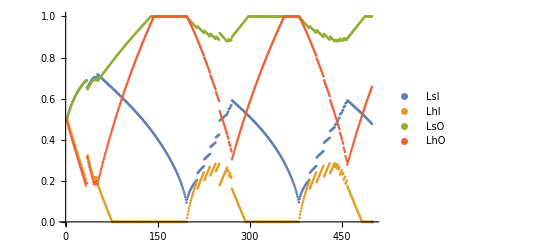

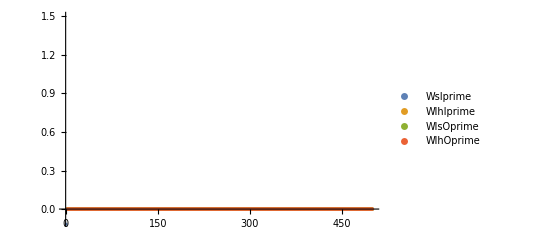

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}}, PlotLegends->{LsI,LhI,LsO,LhO}]
ListPlot[{DlsItab,DlhItab,DlsOtab,DlhOtab},PlotRange->{All,{-.1,1.5}}, PlotLegends->{WsIprime,WlhIprime,WlsOprime,WlhOprime}]
```

```mathematica
lsItab + lsOtab+lhItab +lhOtab
```

{2.,2.00138,2.00276,2.00413,2.0055,2.00685,2.0082,2.00954,2.01088,2.01221,2.01353,2.01484,2.01615,2.01745,2.01874,2.02003,2.0213,2.02257,2.02383,2.02509,2.02633,2.02757,2.0288,2.03002,2.03124,2.03245,2.03364,2.03483,2.03602,2.03719,2.03835,2.03951,2.04066,2.0418,2.04293,2.04405,2.04516,2.04626,2.04736,2.04844,2.04952,2.05058,2.05164,2.05268,2.05372,2.05475,2.05577,2.05677,2.05777,2.05876,2.05973,2.0607,2.06166,2.0626,2.06353,2.06446,2.06537,2.06627,2.06716,2.06804,2.0689,2.06975,2.0706,2.07143,2.07224,2.07305,2.07384,2.07462,2.07539,2.07614,2.07688,2.07761,2.07833,2.07903,2.07971,2.08038,2.08104,2.08168,2.08231,2.08292,2.08352,2.0841,2.08467,2.08522,2.08575,2.08627,2.08677,2.08726,2.08772,2.08817,2.0886,2.08902,2.08941,2.08979,2.09014,2.09048,2.0908,2.0911,2.09137,2.09163,2.09187,2.09208,2.09227,2.09244,2.09259,2.09271,2.09281,2.09289,2.09294,2.09296,2.09296,2.09294,2.09289,2.09281,2.0927,2.09256,2.0924,2.0922,2.09198,2.09172,2.09143,2.09111,2.09076,2.09037,2.08995,2.08949,2.089,2.08847,2.0879,2.08729,2.08663,2.08594,2.08521,2.08443,2.08361,2.08274,2.08182,2.08085,2.07984,2.07877,2.07765,2.07647,2.07524,2.07395,2.0726,2.07118,2.0697,2.06816,2.06654,2.06486,2.0631,2.06127,2.05935,2.05736,2.05528,2.05311,2.05085,2.04849,2.04603,2.04347,2.04081,2.03803,2.03513,2.03211,2.02897,2.02569,2.02227,2.0187,2.01498,2.0111,2.00705,2.00282,1.9984,2.00301,1.9986,2.00321,1.9988,2.00341,1.99901,2.00361,1.99921,2.0038,1.99941,2.004,1.99961,2.0042,1.99981,2.00439,2.00001,2.00459,2.00021,2.00478,2.00041,2.00498,2.00061,2.00517,2.00081,2.00537,2.00101,2.00556,2.00121,2.00576,2.00141,2.00595,2.0016,2.00614,2.0018,2.00634,2.002,2.00653,2.0022,2.00672,2.00239,2.00691,2.00259,2.00711,2.00279,2.0073,2.00298,2.00749,2.00318,2.00768,2.00337,2.00787,2.00357,2.00806,2.00376,2.00825,2.00396,2.00844,2.00415,2.00863,2.00434,2.00882,2.00454,2.00901,2.00473,2.0092,2.00492,2.00939,2.00512,2.00957,2.00531,2.00976,2.0055,2.00995,2.00569,2.01014,2.00588,2.01032,2.00607,2.01051,2.00627,2.0107,2.00646,2.01088,2.00665,2.01107,2.00684,2.01126,2.00703,2.01144,2.00722,2.01163,2.00741,2.01181,2.00759,2.012,2.00778,2.01218,2.00797,2.01236,2.00816,2.01255,2.00835,2.01273,2.00854,2.01292,2.00872,2.0131,2.00891,2.01328,2.0091,2.01346,2.00928,2.01365,2.00947,2.01383,2.00966,2.01401,2.00984,2.01419,2.01003,2.01437,2.01021,2.01456,2.0104,2.01474,2.01058,2.01492,2.01077,2.0151,2.01095,2.01528,2.01113,2.01546,2.01132,2.01564,2.0115,2.01582,2.01168,2.016,2.01187,2.01617,2.01205,2.01635,2.01223,2.01653,2.01242,2.01671,2.0126,2.01689,2.01278,2.01707,2.01296,2.01724,2.01314,2.01742,2.01332,2.0176,2.0135,2.01777,2.01368,2.01795,2.01386,2.01813,2.01404,2.0183,2.01422,2.01848,2.0144,2.01865,2.01458,2.01883,2.01476,2.01901,2.01494,2.01918,2.01512,2.01935,2.0153,2.01953,2.01548,2.0197,2.01565,2.01988,2.01583,2.02005,2.01601,2.02023,2.01619,2.0204,2.01636,2.02057,2.01654,2.02074,2.01672,2.02092,2.01689,2.02109,2.01707,2.02126,2.01724,2.02143,2.01742,2.02161,2.01759,2.02178,2.01777,2.02195,2.01794,2.02212,2.01812,2.02229,2.01829,2.02246,2.01847,2.02263,2.01864,2.0228,2.01882,2.02297,2.01899,2.02314,2.01916,2.02331,2.01934,2.02348,2.01951,2.02365,2.01968,2.02382,2.01985,2.02399,2.02003,2.02416,2.0202,2.02433,2.02037,2.0245,2.02054,2.02466,2.02071,2.02483,2.02088,2.025,2.02106,2.02517,2.02123,2.02533,2.0214,2.0255,2.02157,2.02567,2.02174,2.02583,2.02191,2.026,2.02208,2.02617,2.02225,2.02633,2.02242,2.0265,2.02258,2.02666,2.02275,2.02683,2.02292,2.027,2.02309,2.02716,2.02326,2.02733,2.02343,2.02749,2.0236,2.02765,2.02376,2.02782,2.02393,2.02798,2.0241,2.02815,2.02426,2.02831,2.02443,2.02847,2.0246,2.02864,2.02476,2.0288,2.02493,2.02896,2.0251,2.02913,2.02526,2.02929,2.02543,2.02945,2.02559,2.02961,2.02576,2.02978,2.02592,2.02994,2.02609,2.0301,2.02625,2.03026,2.02642,2.03042,2.02658,2.03058,2.02675,2.03074,2.02691,2.0309,2.02708,2.03106,2.02724,2.03123,2.0274,2.03139,2.02757,2.03155,2.02773,2.03171,2.02789,0}